# Initialization

```mathematica
CylEqnFastOptimized[l1_,l2_,l3_,z_,opts:OptionsPattern[]]:=Module[{wp=100,L,m,nList,anglesL,anglesR,B,gram,rhsVec,coeffs},L=2 (l1+l2+l3);
m=L/2;
nList=Range[m];
anglesL=N[Join[Table[2 Pi (L/2+l1+1-k)/L,{k,1,l1}],Table[2 Pi (L/2+2 l1+l2+1-k)/L,{k,l1+1,l1+l2}],Table[2 Pi (L+l1+l2+1-k)/L,{k,l1+l2+1,m}]],wp];
anglesR=N[Table[2 Pi k/L,{k,1,m}],wp];

B=Developer`ToPackedArray[Exp[I Outer[Times,anglesL,nList]]+Exp[I Outer[Times,Take[anglesR,Length[anglesL]],nList]],Complex];

gram=Transpose[B].B;
gram[[1,1]]+=SetPrecision[1,wp];
rhsVec=Developer`ToPackedArray[UnitVector[m,1],Complex];

coeffs=LinearSolve[gram,rhsVec];
Chop@Sum[coeffs[[n]] z^(n-1),{n,1,m}]]
η[τ_]:=DedekindEta[τ]
Z[τ_]:= Im[τ]^(-13)Abs[η[τ]]^(-48)
Options[RecCylEqnFastOptimized]={WorkingPrecision->100};
PeriodsFast[l1_,l2_,l3_,m1_,m2_,m3_]:=Module[{L=2(l1+l2+l3),k1=m1,k2=l1+m2,k3=l1+l2+m3,func},
func[z_]=Integrate[CylEqnFastOptimized[l1,l2,l3,z],z]; 
{func[E^(2Pi I (L/2+l1+1-k1)/L)]-func[E^(2Pi I k1/L)],func[E^(2Pi  I(L/2+2l1+l2+1-k2)/L)]-func[E^(2Pi I k2/L)],func[E^(2Pi I (L+l1+l2+1-k3)/L)]-func[E^(2Pi I k3/L)]}
];
PeriodsFastGivenF[l1_,l2_,l3_,m1_,m2_,m3_,f_,z_]:=Module[{L=2(l1+l2+l3),k1=m1,k2=l1+m2,k3=l1+l2+m3,func},
func[w_]=Integrate[f/.{z->w},w]/.A[_]:>0; 
{func[E^(2Pi I (L/2+l1+1-k1)/L)]-func[E^(2Pi I k1/L)],func[E^(2Pi  I(L/2+2l1+l2+1-k2)/L)]-func[E^(2Pi I k2/L)],func[E^(2Pi I (L+l1+l2+1-k3)/L)]-func[E^(2Pi I k3/L)]}
];
IntegralFZ[l1_,l2_,l3_,f_,z_]:=Module[{L=2(l1+l2+l3),funcz},
funcz[w_]=Integrate[(w*(f/. {z->w})^2)/. A[_]:>0,w];
{funcz[E^(2Pi I (L/2+l1)/L)]-funcz[E^(0)],funcz[E^(2Pi  I(L/2+l1)/L)]-funcz[E^(2Pi I (l1+l2)/L)]}
];
computeBothSides[l1_,l2_,l3_,m1_,m2_,m3_]:= Module[{f = CylEqnFastOptimized[l1,l2,l3,z] ,per,fZero, jacobian, τ},
per = PeriodsFastGivenF[l1,l2,l3,m1,m2,m3,f,z];
τ = per[[2]]/per[[1]];
Print[τ];
fZero = Abs[f/per[[1]]]/.{z->0};
jacobian = computePeriodDerivative[l1,l2,l3,m1,m2,m3,1];
{combinedDet[l1,l2,l3],jacobian fZero^(-2) Z[τ]}
]
ToFundamentalDomain[tau0_,maxIter_:1000,tol_:10^-14]:=Module[{tau=N[tau0],n,iter=0},If[Im[tau]<=0,Return[$Failed,Module]];
While[iter<maxIter,iter++;
(*1) Shift by an integer to bring Re[tau] into[-1/2,1/2)*)n=Floor[Re[tau]+1/2];
tau=tau-n;
(*2) If|tau| <1,apply S to push it outside the unit circle*)If[Abs[tau]<1-tol,tau=-1/tau;
Continue[];];
(*3) Boundary stabilization:if very close to boundary,snap consistently*)If[Abs[Abs[tau]-1]<=tol&&Re[tau]<0,tau=-Conjugate[tau]];
(*The above optional step makes the choice on the unit circle consistent.*)(*If we’re in the domain (up to tolerance),stop*)If[Abs[Re[tau]]<=1/2+tol&&Abs[tau]>=1-tol,Break[]];];
If[iter>=maxIter,$Failed,tau]]
computePeriodDerivativePrime[ l1_, l2_,l3_, m1_,m2_,m3_, ϵ_]:=
Module[{periodsLp, periodsLm,periodsRp, periodsRm, τL, τR, L = 2(l1 + l2 + l3), ϵN},
periodsLp = PeriodsFast[l1 + ϵ,l2,l3 - ϵ, m1,m2,m3];
periodsLm = PeriodsFast[l1 - ϵ,l2,l3 + ϵ,m1,m2,m3];
periodsRp = PeriodsFast[l1,l2 + ϵ,l3 - ϵ,m1,m2,m3];
periodsRm = PeriodsFast[l1,l2-ϵ,l3 + ϵ,m1,m2,m3];
τL =periodsLp[[2]]/periodsLp[[1]]-periodsLm[[2]]/periodsLm[[1]];
τR = periodsRp[[2]]/periodsRp[[1]]-periodsRm[[2]]/periodsRm[[1]];
ϵN = ϵ/(L/2);
1/(4ϵN^2)(τL Conjugate[τR]-Conjugate[τL]τR)
];
computePeriodDerivative[ l1_, l2_,l3_, m1_,m2_,m3_, ϵ_]:=
Module[{periodsLp, periodsLm,periodsRp, periodsRm, τL, τR, L = 2(l1 + l2 + l3), ϵN},
periodsLp = PeriodsFast[l1 + ϵ,l2,l3 - ϵ, m1,m2,m3];
periodsLm = PeriodsFast[l1 - ϵ,l2,l3 + ϵ,m1,m2,m3];
periodsRp = PeriodsFast[l1,l2 + ϵ,l3 - ϵ,m1,m2,m3];
periodsRm = PeriodsFast[l1,l2-ϵ,l3 + ϵ,m1,m2,m3];
τL = ToFundamentalDomain[periodsLp[[2]]/periodsLp[[1]]]-ToFundamentalDomain[periodsLm[[2]]/periodsLm[[1]]];
τR =ToFundamentalDomain[ periodsRp[[2]]/periodsRp[[1]]]-ToFundamentalDomain[periodsRm[[2]]/periodsRm[[1]]];
ϵN = ϵ/(L/2);
1/(4ϵN^2)(τL Conjugate[τR]-Conjugate[τL]τR)
];
Bmat[L_,l1_,l2_]:=Module[{k1,k2,k3},N[Join[Table[Table[E^(2Pi I m k1/L)-E^(2Pi I m/L (L/2+l1+1-k1)),{m,1,L/2}],{k1,1,l1}],Table[Table[E^(2Pi I m k2/L)-E^(2Pi I m/L (L/2+2l1+l2+1-k2)),{m,1,L/2}],{k2,l1+1,l1+l2}],Table[Table[E^(2Pi I m k3/L)-E^(2Pi I m/L (L+l1+l2+1-k3)),{m,1,L/2}],{k3,l1+l2+1,L/2}]],prec]];
Bdet[L_,l1_,l2_]:=Abs[Det[Bmat[L,l1,l2]]]^2/64^L;
primeDet[L_, l1_,l2_]:= Exp[logDetCholesky[DirectRedTracedMat[L,l1,l2, DirectMatNFast[L,prec]]]]/(L/2);
combinedDet[l1_,l2_,l3_]:=Abs[Bdet[2(l1+l2+l3),l1,l2]] primeDet[2(l1+l2+l3),l1,l2]^(-13);
combinedDet2[l1_,l2_,l3_]:={Abs[Bdet[2(l1+l2+l3),l1,l2]] ,primeDet[2(l1+l2+l3),l1,l2]^(-13)};
computeTau[l1_,l2_,l3_,m1_,m2_,m3_]:=With[{per = PeriodsFast[l1,l2,l3, m1, m2,m3]}, per[[2]]/per[[1]]];
computeRHS[l1_,l2_,l3_,m1_,m2_,m3_]:= Module[{f = CylEqnFastOptimized[l1,l2,l3,z] ,per,fZero, jacobian, τ,f2,b},
per = PeriodsFastGivenF[l1,l2,l3,m1,m2,m3,f,z];
τ = per[[2]]/per[[1]];
fZero = Abs[f/per[[1]]]/.{z->0};
(*normalize f by the period along the alpha cycle such that *)
f2[c_]:=f/. z->c;
b=PoleInterceptAverage[f2,l1,l2,l3];
jacobian = computePeriodDerivativePrime[l1,l2,l3,m1,m2,m3,1];
{  fZero ^(-2) ,η[τ],Im[τ],b,jacobian,τ,per[[1]]}
]
```

# Computation

```mathematica
(*Order of values returned is: bcDet (1),matterDet (2),fZero^(-2) (3),eta(tau) (4),Im(tau) (5),b_i (6),jacobian (7),tau (8),period (9)*)
(*1,2,3,4 are just 4 different values of l_i, with 1, 2 being related by modular transformation and the others are genuinely different*)data1=Table[Module[{numDet,denDet,rhsNum,rhsDen},numDet=combinedDet2[3(k+1),(k+1),9 (k+1)];
denDet=combinedDet2[5 (k+1),7 (k+1),(k+1)];
rhsNum=computeRHS[3 k,k,9 k,Round[3 k/2],Round[k/2],Round[9 k/2]];
rhsDen=computeRHS[5 k,7 k,k,Round[5 k/2],Round[7 k/2],Round[k/2]];
{numDet[[1]]/denDet[[1]],numDet[[2]]/denDet[[2]],rhsNum[[1]]/rhsDen[[1]],rhsNum[[2]]/rhsDen[[2]],rhsNum[[3]]/rhsDen[[3]],Exp[3/2*rhsNum[[4]]]/Exp[3/2*rhsDen[[4]]],rhsNum[[5]]/rhsDen[[5]],rhsNum[[6]],rhsNum[[7]]}],{k,1,30,2}];
```

```mathematica
data2=Table[Module[{numDet,denDet,rhsNum,rhsDen},numDet=combinedDet2[9(k+1),3(k+1),1 (k+1)];
denDet=combinedDet2[5 (k+1),7 (k+1),(k+1)];
rhsNum=computeRHS[9k,3k,1 k,Round[ 9k/2],Round[3k/2],Round[ 1k/2]];rhsDen=computeRHS[5 k,7 k,k,Round[5 k/2],Round[7 k/2],Round[k/2]];
{numDet[[1]]/denDet[[1]],numDet[[2]]/denDet[[2]],rhsNum[[1]]/rhsDen[[1]],rhsNum[[2]]/rhsDen[[2]],rhsNum[[3]]/rhsDen[[3]],Exp[3/2*rhsNum[[4]]]/Exp[3/2*rhsDen[[4]]],rhsNum[[5]]/rhsDen[[5]],rhsNum[[6]],rhsNum[[7]]}],{k,1,30,2}];
```

```mathematica
data3=Table[Module[{numDet,denDet,rhsNum,rhsDen},numDet=combinedDet2[7(k+1),7(k+1),1 (k+1)];
denDet=combinedDet2[9 (k+1),5 (k+1),(k+1)];
rhsNum=computeRHS[7k,7k,1 k,Round[ 7k/2],Round[7k/2],Round[ 1k/2]];
rhsDen=computeRHS[9 k,5k,k,Round[9 k/2],Round[5 k/2],Round[k/2]];
{numDet[[1]]/denDet[[1]],numDet[[2]]/denDet[[2]],rhsNum[[1]]/rhsDen[[1]],rhsNum[[2]]/rhsDen[[2]],rhsNum[[3]]/rhsDen[[3]],Exp[3/2*rhsNum[[4]]]/Exp[3/2*rhsDen[[4]]],rhsNum[[5]]/rhsDen[[5]],rhsNum[[6]],rhsNum[[7]]}],{k,1,30,2}];
data4=Table[Module[{numDet,denDet,rhsNum,rhsDen},numDet=combinedDet2[7(k+1),5(k+1),3 (k+1)];
denDet=combinedDet2[9 (k+1),5 (k+1),(k+1)];
rhsNum=computeRHS[7k,5k,3 k,Round[ 7k/2],Round[5k/2],Round[ 3k/2]];
rhsDen=computeRHS[9 k,5k,k,Round[9 k/2],Round[5 k/2],Round[k/2]];
{numDet[[1]]/denDet[[1]],numDet[[2]]/denDet[[2]],rhsNum[[1]]/rhsDen[[1]],rhsNum[[2]]/rhsDen[[2]],rhsNum[[3]]/rhsDen[[3]],Exp[3/2*rhsNum[[4]]]/Exp[3/2*rhsDen[[4]]],rhsNum[[5]]/rhsDen[[5]],rhsNum[[6]],rhsNum[[7]]}],{k,1,30,2}];
```

```mathematica
k=29;
l1=3(k+1);
l2=(k+1);
l3=9 (k+1);
Log[primeDet[2(l1+l2+l3),l1,l2]^(-13)]
```

-91.37225995821335143498904275186642138541299784306648670664640304113526457364436706820996379106079

```mathematica
η[0.8625102695981686+0.695666726210055 ⅈ]/η[0.15633035485768704+0.8830953809007003 ⅈ]
```

```mathematica
η[0.86214046+0.69386175I]/η[0.15598630935885463+0.8822301889920067 I]
```

1.02377+0.20553 ⅈ

```mathematica
k=29;
combinedDet2[3(k+1),(k+1),9 (k+1)]/combinedDet2[5(k+1),7(k+1),1 (k+1)]
```

{1.16381068989617716194999705632716248935055262026137121221724163010338255822978184045036775623360852,3.1061172734007071685362704932794785023425649007540372314078776349534535485947751533367125480678}

```mathematica
(*Order of values returned is: bcDet (1),matterDet (2),fZero^(-2) (3),eta(tau) (4),Im(tau) (5),b_i (6),jacobian (7),tau (8),period (9)*)
data1[[All,6]]
```

{1.80293,1.53458,1.28449,1.24748,1.23343,1.22632,1.22216,1.2195,1.21769,1.21639,1.21543,1.2147,1.21413,1.21368,1.21331}

```mathematica
(*Build the CylEqn function*)L=13*2*15;          (* =234*)
l1=3*15;            (* =9*)
l2=1*15;            (* =81*)
l3=L/2-l1-l2;  (*if you need it;not used directly below*)

fnum=CylEqnFastOptimized[l1,l2,l3,z,"WorkingPrecision"->100];  
fnum2=CylEqn[l1,l2,l3,z];  (*this is an expression in z*)
```

```mathematica
coeffsM=CoefficientList[fnum,z];
N[coeffsM,30]//Short
coeffPairs=({Re[#],Im[#]}&/@coeffsM);
Export["coeffsM.json",coeffPairs,"JSON"];
```

{1.,0,«111»,0,-0.150576-0.0440493 ⅈ}

Best fit parameters: {-0.184153,-0.336078}

Intercept a = -0.184153

Slope b = -0.336078

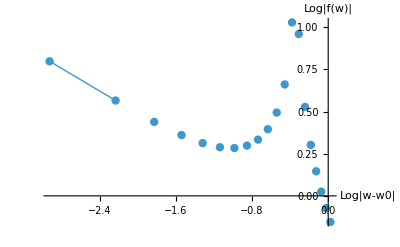

```mathematica
(*Parameters*)
(*Parameters*)alphaMin=-40;
alphaMax=0;
step=2;
fitLow=-4;
fitHigh=-1;
ell=l1;

w0=Exp[I Pi (2.0 ell+1.0)/L];

(*Build log-log data:{Log|w-w0|,Log|f(w)|} for each alpha*)
vals=Table[Module[{w,fw,dx,dy},w=Exp[I Pi (2.0 ell/L+2.0 alpha/L+1.0/L)];
fw=(fnum/. z->w);
dx=Abs[w-w0];
dy=Abs[fw];
{alpha,Log[dx],Log[dy]}],{alpha,alphaMin,alphaMax,step}];

(*Drop any non-finite points (e.g.Log[0]->-Infinity)*)
valsFinite=Select[vals,FreeQ[#,ComplexInfinity|Indeterminate|Infinity|-Infinity]&];

(*Points used for the fit window*)
fitData=({#[[2]],#[[3]]}&/@Select[valsFinite,fitLow<=#[[1]]<=fitHigh&]);

(*Linear fit y=a+b x*)
lm=LinearModelFit[fitData,x,x];

params=lm["BestFitParameters"];  (*<|Intercept->a,x->b|> or {a,b} depending on version*)
Print["Best fit parameters: ",params];

(*Extract intercept and slope robustly*)
a=lm["BestFitParameters"][[1]];
b=lm["BestFitParameters"][[2]];
Print["Intercept a = ",a];
Print["Slope b = ",b];

(*Plot:all points+best fit line over the fit-x range*)
xMin=Min[fitData[[All,1]]];
xMax=Max[fitData[[All,1]]];

Show[ListPlot[({#[[2]],#[[3]]}&/@valsFinite),PlotStyle->PointSize[0.015],AxesLabel->{"Log|w-w0|","Log|f(w)|"},PlotRange->All],Plot[lm[x],{x,xMin,xMax},PlotStyle->{Thick}]]
```

```mathematica
L
```

234

```mathematica
fnum/.z->Exp[4*I*(1+1)Pi/L]
fnum2/.z->Exp[4*I*(1+1)Pi/L]
```

1.23602+0.231557 ⅈ

(1.23601780631249+0.23155729296807 ⅈ)+ⅇ^(-(4 ⅈ π)/117) A[117.]

```mathematica
fnum/.z->0.5
fnum2/.z->0.5
```

1.07269-0.149775 ⅈ

(1.07269-0.149775 ⅈ)+1.20371×10^-35 A[117.]

```mathematica
poly=CylEqnFastOptimized[l1,l2,l3,z,"WorkingPrecision"->100];
coeffsM=CoefficientList[poly,z];  (*length m*)
N[coeffsM,30]//Short
```

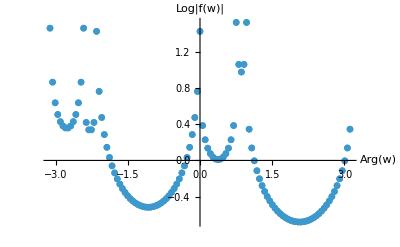

```mathematica
(*choose L and fnum beforehand*)(*Example:L=234;
fnum=CylEqnFastOptimized[l1,l2,l3,z]/. A[_]->0;*)xMax=L-1;

vals=Table[Module[{w,fw},w=Exp[4 I Pi (x+1)/L];
fw=fnum/. z->w;
{Arg[w],Log[Abs[fw]]}],{x,0,xMax,1}];

(*Sort by Arg so the plot is ordered nicely*)
valsSorted=SortBy[Select[vals,FreeQ[#,Indeterminate|ComplexInfinity|Infinity|-Infinity]&],First];

ListPlot[valsSorted,PlotStyle->PointSize[0.012],AxesLabel->{"Arg(w)","Log|f(w)|"},PlotRange->All]
```

```mathematica
vals=IntegralFZ[l1,l2,l3,fnum,z]
```

$Aborted

jacobian

```mathematica
Re[vals[[1]]*vals[[2]]]
```

-0.496647

```mathematica
η[0.8625102695981686+0.695666726210055 ⅈ]
η[0.86214046+0.69386175I]
```

0.803867+0.19302 ⅈ

0.804185+0.193128 ⅈ

```mathematica
L=13*30*2;
l1=3*30;
l2=1*30;
testMat=DirectRedTracedMat[L,l1,l2, DirectMatNFast[L,prec]];
L=13*30*2;
l1=5*30;
l2=7*30;
testMat2=DirectRedTracedMat[L,l1,l2, DirectMatNFast[L,prec]];
```

```mathematica
logDetCholesky[testMat]-Log[L/2]
logDetCholesky[testMat2]-Log[L/2]
```

7.028635381401027033460695596297417029647153680235883592818954080087328044126489774477689522389291

7.115817956867551093315493825334823921356145590660663075074401157713048024104788486167413534958057

```mathematica
data1[[All,2]]
```

{3.02336153792151617717793638196442884950704781567331009418842782832614752330776446897147248931866,3.07431692328843911331272749684808229471034800256324657240211338521018764809697943991484646982073,3.08853262661578960807537450225561119087390092778811365844964184209169967879778010739118720583524,3.0948706675641157704655820652465599758880277304040289410479790033756896589623572980180562231151,3.0983635942737186997947561111667946289117970332070388476891865605562430262251401809492744530185,3.1005398517194316798261581756375170881301759290508784183304266450805540832045246627090347650159,3.1020093052353209788334941823409235644837916436034579590400279029837914393976354802571149403946,3.103059604051323759323224836093511466617047052388126522369720733522868310971651387480524545573,3.1038428463008456184367537847515095744429734444933145902199155935892195971461733610552077273739,3.1044464557684602810709399613432064468080315680121743261826258295455481703024119793768384264564,3.104923992728335005200770429445593266591971733088329964180732296722508158582929167946024912864,3.1053099683880463942435229743733664393227881243909634916523257340155026107855994711657029361578,3.1056275485271721562392176465246992580879461620530262232215189197570188098744920320096970246662,3.1058928191435240275135072528761403901725800222081562485396065199084455587080426925477041701695,3.1061172734007071685362704932794785023425649007540372314078776349534535485947751533367125480678}

```mathematica
(*Order of values returned from "data" is: bcDet (1),matterDet (2),fZero^(-2) (3),eta(tau) (4),Im(tau) (5),b_i (6),jacobian (7),tau (8),period (9)*)
matterDet1=data1[[All,2]];
bcDet1=data1[[All,1]];
(*"Guess" is what the matterDet should be, given the standard calculation in eq. 7.9*)
eq79Guess1= Abs[data1[[All,5]]]^(-13)*Abs[data1[[All,4]]]^(-52)*(data1[[All,6]]^(26/18));
(*"Actual" is what it the function to be*)
eq79Actual1 = data1[[All,3]]*data1[[All,7]]*Abs[data1[[All,5]]]^(-13)*Abs[data1[[All,4]]]^(-48);
eq79GuessBC1=data1[[All,3]]*data1[[All,7]]*Abs[data1[[All,4]]]^(4)/(data2[[All,6]]^(26/18));
(*For now, "actual bc" doesn't mean anything, I'm just playing around with various functions to guess*)
eq79ActualBC1=data1[[All,3]]*(Abs[data1[[All,9]]])^(-2)*Abs[data1[[All,4]]]^(4)*data1[[All,6]]^(8/3)/(data1[[All,6]]^(26/18));

(*The same but for modular transformation*)
matterDet2=data2[[All,2]];
bcDet2=data2[[All,1]];
(*Guess is what the matterDet should be, given the standard calculation in eq. 7.9*)
eq79Guess2=Abs[data2[[All,5]]]^(-13)*Abs[data2[[All,4]]]^(-52)*(data2[[All,6]]^(26/18));
(*Actual is what it seems to be*)
eq79Actual2= data2[[All,3]]*data2[[All,7]]*Abs[data2[[All,5]]]^(-13)*Abs[data2[[All,4]]]^(-48);
eq79GuessBC2=data2[[All,3]]*data2[[All,7]]*Abs[data2[[All,4]]]^(4)/(data2[[All,6]]^(26/18));
(*For now, "actual bc" doesn't mean anything, I'm just playing around with various functions to guess*)
eq79ActualBC2=data2[[All,3]]*(Abs[data2[[All,9]]])^(-2)*data2[[All,7]]*Abs[data2[[All,4]]]^(4)*data2[[All,6]]^(2/3)/(data2[[All,6]]^(26/18));

(*Different l_i values*)
matterDet3=data3[[All,2]];
bcDet3=data3[[All,1]];
(*Guess is what the matterDet should be, given the standard calculation in eq. 7.9*)
eq79Guess3= Abs[data3[[All,5]]]^(-13)*Abs[data3[[All,4]]]^(-52)*(data3[[All,6]]^(26/18));
(*Actual is what it seems to be*)
eq79Actual3= data3[[All,3]]*data3[[All,7]]*Abs[data3[[All,5]]]^(-13)*Abs[data3[[All,4]]]^(-48);
eq79GuessBC3=data3[[All,3]]*data3[[All,7]]*Abs[data3[[All,4]]]^(4)/(data2[[All,6]]^(26/18));
eq79ActualBC3=data3[[All,3]]*data3[[All,6]]^(4/3);

(*Different l_i values*)
matterDet4=data4[[All,2]];
bcDet4=data4[[All,1]];
(*Guess is what the matterDet should be, given the standard calculation in eq. 7.9*)
eq79Guess4=Abs[data4[[All,5]]]^(-13)*Abs[data4[[All,4]]]^(-52)*(data4[[All,6]]^(26/18));
(*Actual is what it seems to be*)
eq79Actual4= data4[[All,3]]*data4[[All,7]]*Abs[data4[[All,5]]]^(-13)*Abs[data4[[All,4]]]^(-48);
eq79GuessBC4=data4[[All,3]]*data4[[All,7]]*Abs[data4[[All,4]]]^(4)/(data2[[All,6]]^(26/18));
eq79ActualBC4=data4[[All,3]]*data4[[All,7]]*Abs[data4[[All,4]]]^(4)*data4[[All,6]]^(4/3);
```

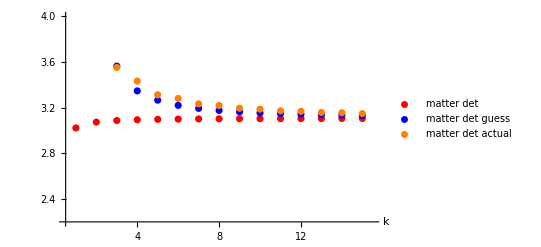

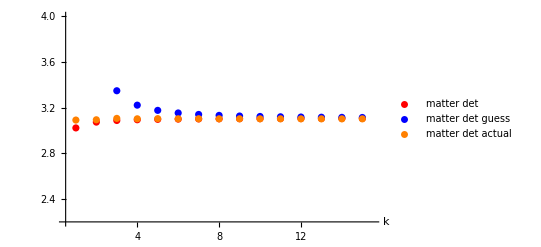

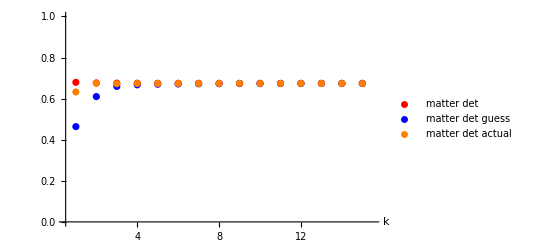

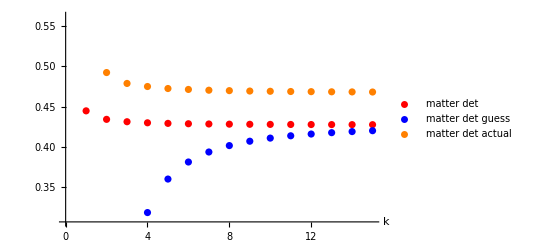

```mathematica
(*Plot of matter determinant against what it should be vs. what it actually is analytically*)
ListPlot[{matterDet1,eq79Guess1,eq79Actual1},PlotStyle->{Red,Blue,Orange,Green,Purple,Black},AxesLabel->{"k",None},PlotRange->{{0.5,15.5},{2.2,4}},PlotLegends->Placed[{"matter det","matter det guess","matter det actual"},Right]]
ListPlot[{matterDet2,eq79Guess2,eq79Actual2},PlotStyle->{Red,Blue,Orange,Green,Purple,Black},AxesLabel->{"k",None},PlotRange->{{0.5,15.5},{2.2,4}},PlotLegends->Placed[{"matter det","matter det guess","matter det actual"},Right]]
ListPlot[{matterDet3,eq79Guess3,eq79Actual3},PlotStyle->{Red,Blue,Orange,Green,Purple,Black},AxesLabel->{"k",None},PlotRange->{{0.5,15.5},{0.0,1.0}},PlotLegends->Placed[{"matter det","matter det guess","matter det actual"},Right]]
ListPlot[{matterDet4,eq79Guess4,eq79Actual4},PlotStyle->{Red,Blue,Orange,Green,Purple,Black},AxesLabel->{"k",None},PlotLegends->Placed[{"matter det","matter det guess","matter det actual"},Right]]
```

```mathematica
1/Abs[data1[[All,5]]]
```

{1.61236,1.29492,1.28354,1.27719,1.27482,1.27309,1.27214,1.27138,1.27089,1.27047,1.27018,1.26992,1.26973,1.26956,1.26942}

```mathematica
(*Order of values returned from "data" is: bcDet (1),matterDet (2),fZero^(-2) (3),eta(tau) (4),Im(tau) (5),b_i (6),jacobian (7),tau (8),period (9)*)
eq79GuessBC1=data1[[All,3]]*data1[[All,7]]*Abs[data1[[All,4]]]^(4)/(data2[[All,6]]^(26/18));
(*For now, "actual bc" doesn't mean anything, I'm just playing around with various functions to guess*)
eq79ActualBC1=data1[[All,3]]*Abs[data1[[All,4]]]^(4)*Abs[data1[[All,5]]]^(2)/(data1[[All,6]]^(26/18));
```

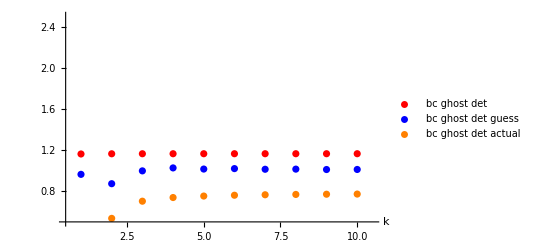

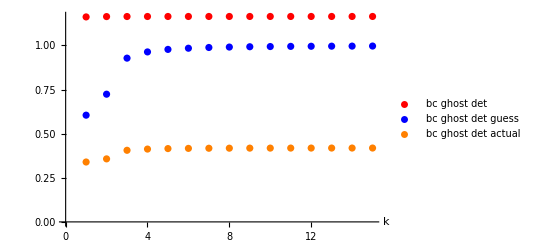

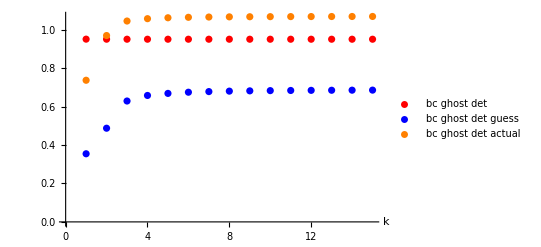

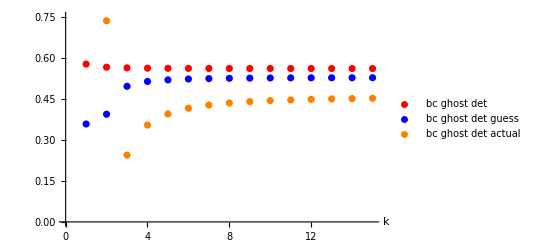

```mathematica
(*Plot of matter determinant against what it should be vs. what it actually is analytically*)
(*At the moment, "bc ghost det actual" doesn't mean anything, but rather reflects a second guess*)
ListPlot[{bcDet1,eq79GuessBC1,eq79ActualBC1},PlotStyle->{Red,Blue,Orange,Green,Purple,Black},AxesLabel->{"k",None},PlotRange->{{0.5,10.5},{0.5,2.5}},PlotLegends->Placed[{"bc ghost det","bc ghost det guess","bc ghost det actual"},Right]]
ListPlot[{bcDet2,eq79GuessBC2,eq79ActualBC2},PlotStyle->{Red,Blue,Orange,Green,Purple,Black},AxesLabel->{"k",None},PlotLegends->Placed[{"bc ghost det","bc ghost det guess","bc ghost det actual"},Right]]
ListPlot[{bcDet3,eq79GuessBC3,eq79ActualBC3},PlotStyle->{Red,Blue,Orange,Green,Purple,Black},AxesLabel->{"k",None},PlotLegends->Placed[{"bc ghost det","bc ghost det guess","bc ghost det actual"},Right]]
ListPlot[{bcDet4,eq79GuessBC4,eq79ActualBC4},PlotStyle->{Red,Blue,Orange,Green,Purple,Black},AxesLabel->{"k",None},PlotLegends->Placed[{"bc ghost det","bc ghost det guess","bc ghost det actual"},Right]]
```

```mathematica
(*Order of values returned from "data" is: bcDet (1),matterDet (2),fZero^(-2) (3),eta(tau) (4),Im(tau) (5),b_i (6),jacobian (7),tau (8),period (9)*)
```

```mathematica
guessingBC1=data1[[All,1]]/(data1[[All,3]]*data1[[All,7]]*Abs[data1[[All,4]]]^(4)/(data2[[All,6]]^(26/18)));
```

# Testing τ dependence by hand

```mathematica
n=400;

triples=Reverse[IntegerPartitions[n,{3},Range[2,n,2]]];   (*each is {a,b,c} with a>=b>=c*)
rhsArray=ConstantArray[0.,{Length[triples]}];
lhsArray=ConstantArray[0.,{Length[triples]}];
```

```mathematica
(*manually abort this at some iteration, usually around 30*)
For[i=1,i<=Length[triples],i++,{a,b,c}=triples[[i*10]];
j=i*10;
lhsNum={Abs[Bdet[2 n,a,b]],primeDet[2 n,a,b]^(-13)};
rhsNum=computeRHS[a+1,b+1,c+1,Round[(a+1)/2],Round[(b+1)/2],Round[(c+1)/2]];
If[Mod[i,10]==0,Print[i]];
rhsArray[[i]]=rhsNum;
lhsArray[[i]]=lhsNum;]
```

10

20

30

$Aborted

```mathematica
rhsNum
```

{3.44683,0.775869+0.0540699 ⅈ,0.961522,-0.529445,0.-4.12685 ⅈ,0.274729+0.961522 ⅈ,-1.41244-1.20492 ⅈ}

```mathematica
(*output of lhsArray is: bdet, matter det*)
(*output of rhsArray is: fZero ^(-2)(1) ,η[τ] (2),Im[τ] (3),b (4),jacobian (5),τ (6),per[[1]] (7)*)
numIter=25
denom=Abs[rhsArray[[1,2]]]^(-52)*Abs[rhsArray[[1,3]]]^(-13)*(Exp[3/2*rhsArray[[1,4]]]^(26/18));
whatMatterShouldbe=Re[Table[{Abs[rhsArray[[i,2]]]^(-52)*Abs[rhsArray[[i,3]]]^(-13)*(Exp[3/2*rhsArray[[i,4]]]^(26/18))/(denom)},{i,numIter}]];
denom=lhsArray[[1,2]];
whatMatterIs=Table[{lhsArray[[i,2]]/denom},{i,numIter}];
dataRHSMatter=Table[{Re[rhsArray[[i,6]]],whatMatterShouldbe[[i]][[1]]},{i,numIter}];
dataLHSMatter=Table[{Re[rhsArray[[i,6]]],whatMatterIs[[i]][[1]]},{i,numIter}];
denom=rhsArray[[1,1]]*rhsArray[[1,5]]*Abs[rhsArray[[1,2]]]^(4)/(Abs[rhsArray[[1,6]]]^(26/18))
whatBCshouldbe=Table[{rhsArray[[i,1]]*rhsArray[[i,5]]*Abs[rhsArray[[i,2]]]^(4)/(Abs[rhsArray[[i,6]]]^(26/18))/denom},{i,numIter}];
whatBCshouldbe2=Table[{rhsArray[[i,1]]*rhsArray[[i,5]]*Abs[rhsArray[[i,2]]]^(4)Abs[rhsArray[[i,6]]]^(8/3)/(Abs[rhsArray[[i,6]]]^(26/18))/denom},{i,numIter}];
denom=lhsArray[[1,1]];
whatBCis=Table[{lhsArray[[i,1]]/denom},{i,numIter}];
dataRHSBC=Table[{Re[rhsArray[[i,6]]],whatBCshouldbe[[i]][[1]]},{i,numIter}];
dataRHSBC2=Table[{Re[rhsArray[[i,6]]],whatBCshouldbe2[[i]][[1]]},{i,numIter}];
dataLHSBC=Table[{Re[rhsArray[[i,6]]],whatBCis[[i]][[1]]},{i,numIter}];
```

25

0.-4.34982 ⅈ

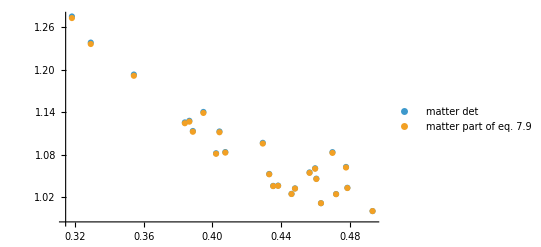

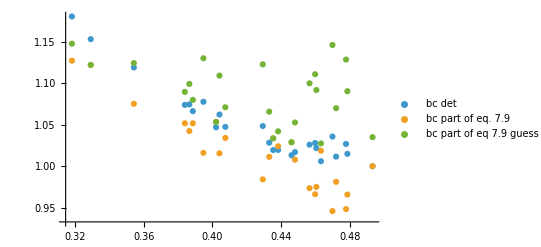

```mathematica
ListPlot[{dataLHSMatter,dataRHSMatter},PlotLegends->{"matter det", "matter part of eq. 7.9"},PlotRange->All]
ListPlot[{dataLHSBC,dataRHSBC,dataRHSBC2},PlotLegends->{"bc det", "bc part of eq. 7.9","bc part of eq 7.9 guess 2"},PlotRange->All]
```